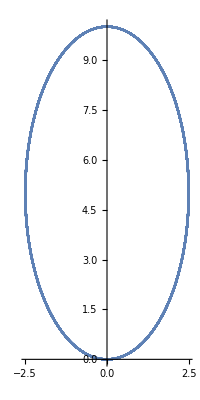

```mathematica
ClearAll["Global`*"];
m=1;mm=1;v0=30;g=10;r=5;q=1;p=0;te=0;

sol=NDSolveValue[{m v0-mm v0==m x'[t]+mm xx'[t],mm v0^2+m v0^2==2 m y[t]+q (m x'[t]^2+mm xx'[t]^2)+p (m x'[te]^2+mm xx'[te]^2)+m y'[t]^2,q ((x[t]-xx[t])^2+(-r+y[t])^2)+p x''[t]==q r^2+p (1-p),x[0]==0,y[0]==0,xx[0]==0,xx'[0]==-v0,x'[0]==v0,y'[0]==0,WhenEvent[y[t]>=r,{q=0,p=1}],WhenEvent[y[t]<r,{q=1,p=0}],WhenEvent[Abs[y[t]]-r<=0.01,te=t]},{x,y,xx},{t,0,100}];

ParametricPlot[{sol[[1]][t],sol[[2]][t]},{t,0,10}]
```